## grupa 1

#### Zad. 1

```mathematica
f=4 x^10-3/x^8+4/x^(1/4);
g=(Cos[x]-ArcTan[x])/(Tan[x]+ArcCos[x]);
h=Log[(x^2+2 x+2)/(x^2-3 x-3)];
D[f,x]
D[g,x]//Simplify
D[h,x]//Simplify
```

24/x^9-1/x^(5/4)+40 x^9

(-(-ArcTan[x]+Cos[x]) (-1/(√(1-x^2))+Sec[x]^2)+(-1/(1+x^2)-Sin[x]) (ArcCos[x]+Tan[x]))/(ArcCos[x]+Tan[x])^2

-(5 x (2+x))/((-3-3 x+x^2) (2+2 x+x^2))

#### Zad. 2

```mathematica
F[x_]:=(1-x)/(x+2);
F'[x]//Simplify
F''[x]//Simplify
Series[F[x],{x,-1,2}]
Normal[%]//Expand
F[-0.9]
%%/.{x->-0.9}
```

-3/(2+x)^2

6/(2+x)^3

2-3 (x+1)+3 (x+1)^2+O[x+1]^3

2+3 x+3 x^2

1.72727

1.73

#### Zad. 3

2 (3+2 x)^3 (-2+3 x)^5 (19+30 x)

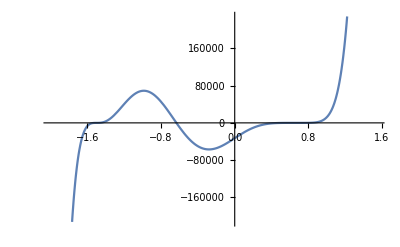

```mathematica
f1=(2x+3)^4(3x-2)^6;
D[f1,x]//Factor
Plot[%,{x,-2,1.55}]
```

## grupa I1

#### Zad. 1

```mathematica
f=5 x^7-3/x^2+4(x^2)^(1/3);
g=(2Log[x]-3Sin[x])/(3^x+2 ArcSin[x]);
h=Cos[Sin[x]] Sin[Cos[x]];
D[f,x]
D[g,x]//Simplify
D[h,x]//Simplify
```

6/x^3+35 x^6+(8 x)/(3 (x^2)^(2/3))

((3^x+2 ArcSin[x]) (2/x-3 Cos[x])-(2/(√(1-x^2))+3^x Log[3]) (2 Log[x]-3 Sin[x]))/((3^x+2 ArcSin[x])^2)

-Cos[Cos[x]] Cos[Sin[x]] Sin[x]-Cos[x] Sin[Cos[x]] Sin[Sin[x]]

#### Zad. 2

```mathematica
F[x_]:=1/(x^2-3);
F'[x]//Simplify
F''[x]//Simplify
Series[F[x],{x,2,2}]
Normal[%]//Expand
F[1.9]
%%/.{x->1.9}
```

-(2 x)/((-3+x^2)^2)

(6 (1+x^2))/((-3+x^2)^3)

1-4 (x-2)+15 (x-2)^2+O[x-2]^3

69-64 x+15 x^2

1.63934

1.55

#### Zad. 3

2 (3+2 x) (-2+x^2)

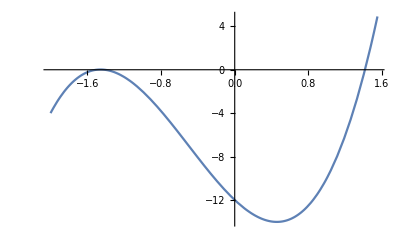

```mathematica
f1=-12 x-4 x^2+2 x^3+x^4;
D[f1,x]//Factor
Plot[%,{x,-2,1.55}]
```